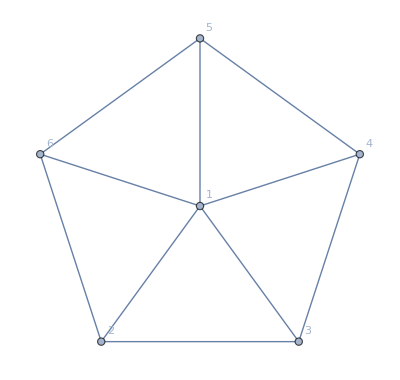

```mathematica
g=WheelGraph[6,VertexLabels->"Name"]
```

```mathematica
gf=Expand[CalculateInOutFormulaMany[g,{{2,3,4,5,6},{1}}]]
```

-30 B1+8 A2 B1-2 A24 B1+2 A24x3 B1-A24x35 B1+A24x35x6 B1-A24x36 B1+A24x36x5 B1-A24x3x5 B1+A24x3x5x6 B1-A24x3x6 B1+A24x5 B1-A24x5x6 B1+A24x6 B1-2 A25 B1+A25x3 B1-A25x36 B1+A25x36x4 B1-A25x3x4 B1+A25x3x46 B1+A25x3x4x6 B1-A25x3x6 B1+A25x4 B1-A25x46 B1-A25x4x6 B1+2 A25x6 B1-4 A2x3 B1+A2x35 B1-A2x35x4 B1+A2x35x46 B1+A2x35x4x6 B1-A2x35x6 B1+2 A2x36 B1-A2x36x4 B1+A2x36x4x5 B1-A2x36x5 B1+2 A2x3x4 B1-A2x3x46 B1+A2x3x46x5 B1-A2x3x4x5 B1+A2x3x4x5x6 B1-A2x3x4x6 B1+A2x3x5 B1-A2x3x5x6 B1+2 A2x3x6 B1-2 A2x4 B1+A2x46 B1-A2x46x5 B1+A2x4x5 B1-A2x4x5x6 B1+A2x4x6 B1-2 A2x5 B1+2 A2x5x6 B1-4 A2x6 B1+8 A3 B1-2 A35 B1+2 A35x4 B1-A35x46 B1-A35x4x6 B1+A35x6 B1-2 A36 B1+A36x4 B1-A36x4x5 B1+A36x5 B1-4 A3x4 B1+A3x46 B1-A3x46x5 B1+2 A3x4x5 B1-A3x4x5x6 B1+A3x4x6 B1-2 A3x5 B1+A3x5x6 B1-2 A3x6 B1+8 A4 B1-2 A46 B1+2 A46x5 B1-4 A4x5 B1+2 A4x5x6 B1-2 A4x6 B1+8 A5 B1-4 A5x6 B1+8 A6 B1

```mathematica
EdgeList[g]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->6,3<->4,4<->5,5<->6}

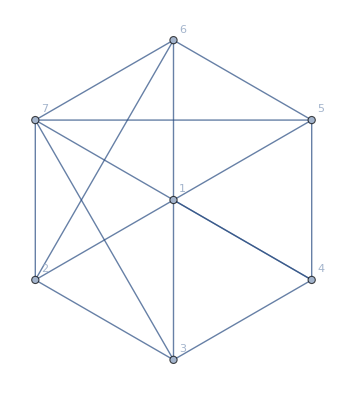

```mathematica
h=EdgeAdd[g,{7<->2,7<->3,7<->4,7<->5,7<->6}]
```

```mathematica
hf=Expand[CalculateInOutFormulaMany[h,{{2,3,4,5,6},{1},{7}}]];
```

```mathematica
Collect[hf,C7]
```

(210-46 A2+10 A24-4 A24x3+A24x35+A24x36+A24x3x5+A24x3x6-3 A24x5+A24x5x6-3 A24x6+10 A25-3 A25x3+A25x36+A25x3x4+A25x3x6-3 A25x4+A25x46+A25x4x6-4 A25x6+14 A2x3-3 A2x35+A2x35x4+A2x35x6-4 A2x36+A2x36x4+A2x36x5-4 A2x3x4+A2x3x46+A2x3x4x5+A2x3x4x6-3 A2x3x5+A2x3x5x6-4 A2x3x6+10 A2x4-3 A2x46+A2x46x5-3 A2x4x5+A2x4x5x6-3 A2x4x6+10 A2x5-4 A2x5x6+14 A2x6-46 A3+10 A35-4 A35x4+A35x46+A35x4x6-3 A35x6+10 A36-3 A36x4+A36x4x5-3 A36x5+14 A3x4-3 A3x46+A3x46x5-4 A3x4x5+A3x4x5x6-3 A3x4x6+10 A3x5-3 A3x5x6+10 A3x6-46 A4+10 A46-4 A46x5+14 A4x5-4 A4x5x6+10 A4x6-46 A5+14 A5x6-46 A6-240 B1+54 A2 B1-12 A24 B1+6 A24x3 B1-2 A24x35 B1+A24x35x6 B1-2 A24x36 B1+A24x36x5 B1-2 A24x3x5 B1+A24x3x5x6 B1-2 A24x3x6 B1+4 A24x5 B1-2 A24x5x6 B1+4 A24x6 B1-12 A25 B1+4 A25x3 B1-2 A25x36 B1+A25x36x4 B1-2 A25x3x4 B1+A25x3x46 B1+A25x3x4x6 B1-2 A25x3x6 B1+4 A25x4 B1-2 A25x46 B1-2 A25x4x6 B1+6 A25x6 B1-18 A2x3 B1+4 A2x35 B1-2 A2x35x4 B1+A2x35x46 B1+A2x35x4x6 B1-2 A2x35x6 B1+6 A2x36 B1-2 A2x36x4 B1+A2x36x4x5 B1-2 A2x36x5 B1+6 A2x3x4 B1-2 A2x3x46 B1+A2x3x46x5 B1-2 A2x3x4x5 B1+A2x3x4x5x6 B1-2 A2x3x4x6 B1+4 A2x3x5 B1-2 A2x3x5x6 B1+6 A2x3x6 B1-12 A2x4 B1+4 A2x46 B1-2 A2x46x5 B1+4 A2x4x5 B1-2 A2x4x5x6 B1+4 A2x4x6 B1-12 A2x5 B1+6 A2x5x6 B1-18 A2x6 B1+54 A3 B1-12 A35 B1+6 A35x4 B1-2 A35x46 B1-2 A35x4x6 B1+4 A35x6 B1-12 A36 B1+4 A36x4 B1-2 A36x4x5 B1+4 A36x5 B1-18 A3x4 B1+4 A3x46 B1-2 A3x46x5 B1+6 A3x4x5 B1-2 A3x4x5x6 B1+4 A3x4x6 B1-12 A3x5 B1+4 A3x5x6 B1-12 A3x6 B1+54 A4 B1-12 A46 B1+6 A46x5 B1-18 A4x5 B1+6 A4x5x6 B1-12 A4x6 B1+54 A5 B1-18 A5x6 B1+54 A6 B1) C7

```mathematica
f1=(-30+8 B2-2 B24+2 B24x3-B24x35+B24x35x6-B24x36+B24x36x5-B24x3x5+B24x3x5x6-B24x3x6+B24x5-B24x5x6+B24x6-2 B25+B25x3-B25x36+B25x36x4-B25x3x4+B25x3x46+B25x3x4x6-B25x3x6+B25x4-B25x46-B25x4x6+2 B25x6-4 B2x3+B2x35-B2x35x4+B2x35x46+B2x35x4x6-B2x35x6+2 B2x36-B2x36x4+B2x36x4x5-B2x36x5+2 B2x3x4-B2x3x46+B2x3x46x5-B2x3x4x5+B2x3x4x5x6-B2x3x4x6+B2x3x5-B2x3x5x6+2 B2x3x6-2 B2x4+B2x46-B2x46x5+B2x4x5-B2x4x5x6+B2x4x6-2 B2x5+2 B2x5x6-4 B2x6+8 B3-2 B35+2 B35x4-B35x46-B35x4x6+B35x6-2 B36+B36x4-B36x4x5+B36x5-4 B3x4+B3x46-B3x46x5+2 B3x4x5-B3x4x5x6+B3x4x6-2 B3x5+B3x5x6-2 B3x6+8 B4-2 B46+2 B46x5-4 B4x5+2 B4x5x6-2 B4x6+8 B5-4 B5x6+8 B6)
```

-30+8 B2-2 B24+2 B24x3-B24x35+B24x35x6-B24x36+B24x36x5-B24x3x5+B24x3x5x6-B24x3x6+B24x5-B24x5x6+B24x6-2 B25+B25x3-B25x36+B25x36x4-B25x3x4+B25x3x46+B25x3x4x6-B25x3x6+B25x4-B25x46-B25x4x6+2 B25x6-4 B2x3+B2x35-B2x35x4+B2x35x46+B2x35x4x6-B2x35x6+2 B2x36-B2x36x4+B2x36x4x5-B2x36x5+2 B2x3x4-B2x3x46+B2x3x46x5-B2x3x4x5+B2x3x4x5x6-B2x3x4x6+B2x3x5-B2x3x5x6+2 B2x3x6-2 B2x4+B2x46-B2x46x5+B2x4x5-B2x4x5x6+B2x4x6-2 B2x5+2 B2x5x6-4 B2x6+8 B3-2 B35+2 B35x4-B35x46-B35x4x6+B35x6-2 B36+B36x4-B36x4x5+B36x5-4 B3x4+B3x46-B3x46x5+2 B3x4x5-B3x4x5x6+B3x4x6-2 B3x5+B3x5x6-2 B3x6+8 B4-2 B46+2 B46x5-4 B4x5+2 B4x5x6-2 B4x6+8 B5-4 B5x6+8 B6

```mathematica
f2=(B24x35x6+B24x36x5+B24x3x5x6+B25x36x4+B25x3x46+B25x3x4x6+B2x35x46+B2x35x4x6+B2x36x4x5+B2x3x46x5+B2x3x4x5x6)
```

B24x35x6+B24x36x5+B24x3x5x6+B25x36x4+B25x3x46+B25x3x4x6+B2x35x46+B2x35x4x6+B2x36x4x5+B2x3x46x5+B2x3x4x5x6

```mathematica
f1-f2 //Simplify//Length
```

71

```mathematica
f1//Simplify//Length
```

82

```mathematica
repBoega=Map[#->Style[#,Red]&,ListofVars[f2]]
```

{B24x35x6→B24x35x6,B24x36x5→B24x36x5,B24x3x5x6→B24x3x5x6,B25x36x4→B25x36x4,B25x3x46→B25x3x46,B25x3x4x6→B25x3x4x6,B2x35x46→B2x35x46,B2x35x4x6→B2x35x4x6,B2x36x4x5→B2x36x4x5,B2x3x46x5→B2x3x46x5,B2x3x4x5x6→B2x3x4x5x6}

```mathematica
f1/.repBoega
```

-30+8 B2-2 B24+2 B24x3-B24x35-B24x36-B24x3x5-B24x3x6+B24x5-B24x5x6+B24x6-2 B25+B25x3-B25x36-B25x3x4-B25x3x6+B25x4-B25x46-B25x4x6+2 B25x6-4 B2x3+B2x35-B2x35x4-B2x35x6+2 B2x36-B2x36x4-B2x36x5+2 B2x3x4-B2x3x46-B2x3x4x5-B2x3x4x6+B2x3x5-B2x3x5x6+2 B2x3x6-2 B2x4+B2x46-B2x46x5+B2x4x5-B2x4x5x6+B2x4x6-2 B2x5+2 B2x5x6-4 B2x6+8 B3-2 B35+2 B35x4-B35x46-B35x4x6+B35x6-2 B36+B36x4-B36x4x5+B36x5-4 B3x4+B3x46-B3x46x5+2 B3x4x5-B3x4x5x6+B3x4x6-2 B3x5+B3x5x6-2 B3x6+8 B4-2 B46+2 B46x5-4 B4x5+2 B4x5x6-2 B4x6+8 B5-4 B5x6+8 B6+B24x35x6+B24x36x5+B24x3x5x6+B25x36x4+B25x3x46+B25x3x4x6+B2x35x46+B2x35x4x6+B2x36x4x5+B2x3x46x5+B2x3x4x5x6

```mathematica
With[{boega=f2},Reduce[f1,boega]]
```

Reduce::ivar: B24x35x6+B24x36x5+B24x3x5x6+B25x36x4+B25x3x46+B25x3x4x6+B2x35x46+B2x35x4x6+B2x36x4x5+B2x3x46x5+B2x3x4x5x6 is not a valid variable.

Reduce[-30+8 B2-2 B24+2 B24x3-B24x35+B24x35x6-B24x36+B24x36x5-B24x3x5+B24x3x5x6-B24x3x6+B24x5-B24x5x6+B24x6-2 B25+B25x3-B25x36+B25x36x4-B25x3x4+B25x3x46+B25x3x4x6-B25x3x6+B25x4-B25x46-B25x4x6+2 B25x6-4 B2x3+B2x35-B2x35x4+B2x35x46+B2x35x4x6-B2x35x6+2 B2x36-B2x36x4+B2x36x4x5-B2x36x5+2 B2x3x4-B2x3x46+B2x3x46x5-B2x3x4x5+B2x3x4x5x6-B2x3x4x6+B2x3x5-B2x3x5x6+2 B2x3x6-2 B2x4+B2x46-B2x46x5+B2x4x5-B2x4x5x6+B2x4x6-2 B2x5+2 B2x5x6-4 B2x6+8 B3-2 B35+2 B35x4-B35x46-B35x4x6+B35x6-2 B36+B36x4-B36x4x5+B36x5-4 B3x4+B3x46-B3x46x5+2 B3x4x5-B3x4x5x6+B3x4x6-2 B3x5+B3x5x6-2 B3x6+8 B4-2 B46+2 B46x5-4 B4x5+2 B4x5x6-2 B4x6+8 B5-4 B5x6+8 B6,B24x35x6+B24x36x5+B24x3x5x6+B25x36x4+B25x3x46+B25x3x4x6+B2x35x46+B2x35x4x6+B2x36x4x5+B2x3x46x5+B2x3x4x5x6]

```mathematica
Simplify[-30+8 B2-2 B24+2 B24x3-B24x35-B24x36-B24x3x5-B24x3x6+B24x5-B24x5x6+B24x6-2 B25+B25x3-B25x36-B25x3x4-B25x3x6+B25x4-B25x46-B25x4x6+2 B25x6-4 B2x3+B2x35-B2x35x4-B2x35x6+2 B2x36-B2x36x4-B2x36x5+2 B2x3x4-B2x3x46-B2x3x4x5-B2x3x4x6+B2x3x5-B2x3x5x6+2 B2x3x6-2 B2x4+B2x46-B2x46x5+B2x4x5-B2x4x5x6+B2x4x6-2 B2x5+2 B2x5x6-4 B2x6+8 B3-2 B35+2 B35x4-B35x46-B35x4x6+B35x6-2 B36+B36x4-B36x4x5+B36x5-4 B3x4+B3x46-B3x46x5+2 B3x4x5-B3x4x5x6+B3x4x6-2 B3x5+B3x5x6-2 B3x6+8 B4-2 B46+2 B46x5-4 B4x5+2 B4x5x6-2 B4x6+8 B5-4 B5x6+8 B6==0]
```

8 B2+2 B24x3+B24x5+B24x6+B25x3+B25x4+2 B25x6+B2x35+2 B2x36+2 B2x3x4+B2x3x5+2 B2x3x6+B2x46+B2x4x5+B2x4x6+2 B2x5x6+8 B3+2 B35x4+B35x6+B36x4+B36x5+B3x46+2 B3x4x5+B3x4x6+B3x5x6+8 B4+2 B46x5+2 B4x5x6+8 B5+8 B6==30+2 B24+B24x35+B24x36+B24x3x5+B24x3x6+B24x5x6+2 B25+B25x36+B25x3x4+B25x3x6+B25x46+B25x4x6+4 B2x3+B2x35x4+B2x35x6+B2x36x4+B2x36x5+B2x3x46+B2x3x4x5+B2x3x4x6+B2x3x5x6+2 B2x4+B2x46x5+B2x4x5x6+2 B2x5+4 B2x6+2 B35+B35x46+B35x4x6+2 B36+B36x4x5+4 B3x4+B3x46x5+B3x4x5x6+2 B3x5+2 B3x6+2 B46+4 B4x5+2 B4x6+4 B5x6

```mathematica
Table[MyLetter[k],{k,16}]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p}

```mathematica
hf//Simplify
```

(210-4 A24x3+A24x35+A24x36+A24x3x5+A24x3x6-3 A24x5+A24x5x6-3 A24x6+10 A25-3 A25x3+A25x36+A25x3x4+A25x3x6-3 A25x4+A25x46+A25x4x6-4 A25x6+14 A2x3-3 A2x35+A2x35x4+A2x35x6-4 A2x36+A2x36x4+A2x36x5-4 A2x3x4+A2x3x46+A2x3x4x5+A2x3x4x6-3 A2x3x5+A2x3x5x6-4 A2x3x6+10 A2x4-3 A2x46+A2x46x5-3 A2x4x5+A2x4x5x6-3 A2x4x6+10 A2x5-4 A2x5x6+14 A2x6-46 A3+10 A35-4 A35x4+A35x46+A35x4x6-3 A35x6+10 A36-3 A36x4+A36x4x5-3 A36x5+14 A3x4-3 A3x46+A3x46x5-4 A3x4x5+A3x4x5x6-3 A3x4x6+10 A3x5-3 A3x5x6+10 A3x6-46 A4+10 A46-4 A46x5+14 A4x5-4 A4x5x6+10 A4x6-46 A5+14 A5x6-46 A6-240 B1+6 A24x3 B1-2 A24x35 B1+A24x35x6 B1-2 A24x36 B1+A24x36x5 B1-2 A24x3x5 B1+A24x3x5x6 B1-2 A24x3x6 B1+4 A24x5 B1-2 A24x5x6 B1+4 A24x6 B1-12 A25 B1+4 A25x3 B1-2 A25x36 B1+A25x36x4 B1-2 A25x3x4 B1+A25x3x46 B1+A25x3x4x6 B1-2 A25x3x6 B1+4 A25x4 B1-2 A25x46 B1-2 A25x4x6 B1+6 A25x6 B1-18 A2x3 B1+4 A2x35 B1-2 A2x35x4 B1+A2x35x46 B1+A2x35x4x6 B1-2 A2x35x6 B1+6 A2x36 B1-2 A2x36x4 B1+A2x36x4x5 B1-2 A2x36x5 B1+6 A2x3x4 B1-2 A2x3x46 B1+A2x3x46x5 B1-2 A2x3x4x5 B1+A2x3x4x5x6 B1-2 A2x3x4x6 B1+4 A2x3x5 B1-2 A2x3x5x6 B1+6 A2x3x6 B1-12 A2x4 B1+4 A2x46 B1-2 A2x46x5 B1+4 A2x4x5 B1-2 A2x4x5x6 B1+4 A2x4x6 B1-12 A2x5 B1+6 A2x5x6 B1-18 A2x6 B1+54 A3 B1-12 A35 B1+6 A35x4 B1-2 A35x46 B1-2 A35x4x6 B1+4 A35x6 B1-12 A36 B1+4 A36x4 B1-2 A36x4x5 B1+4 A36x5 B1-18 A3x4 B1+4 A3x46 B1-2 A3x46x5 B1+6 A3x4x5 B1-2 A3x4x5x6 B1+4 A3x4x6 B1-12 A3x5 B1+4 A3x5x6 B1-12 A3x6 B1+54 A4 B1-12 A46 B1+6 A46x5 B1-18 A4x5 B1+6 A4x5x6 B1-12 A4x6 B1+54 A5 B1-18 A5x6 B1+54 A6 B1-2 A24 (-5+6 B1)+A2 (-46+54 B1)) C7

```mathematica
gf//Simplify
```

(-30+8 A2-2 A24+2 A24x3-A24x35+A24x35x6-A24x36+A24x36x5-A24x3x5+A24x3x5x6-A24x3x6+A24x5-A24x5x6+A24x6-2 A25+A25x3-A25x36+A25x36x4-A25x3x4+A25x3x46+A25x3x4x6-A25x3x6+A25x4-A25x46-A25x4x6+2 A25x6-4 A2x3+A2x35-A2x35x4+A2x35x46+A2x35x4x6-A2x35x6+2 A2x36-A2x36x4+A2x36x4x5-A2x36x5+2 A2x3x4-A2x3x46+A2x3x46x5-A2x3x4x5+A2x3x4x5x6-A2x3x4x6+A2x3x5-A2x3x5x6+2 A2x3x6-2 A2x4+A2x46-A2x46x5+A2x4x5-A2x4x5x6+A2x4x6-2 A2x5+2 A2x5x6-4 A2x6+8 A3-2 A35+2 A35x4-A35x46-A35x4x6+A35x6-2 A36+A36x4-A36x4x5+A36x5-4 A3x4+A3x46-A3x46x5+2 A3x4x5-A3x4x5x6+A3x4x6-2 A3x5+A3x5x6-2 A3x6+8 A4-2 A46+2 A46x5-4 A4x5+2 A4x5x6-2 A4x6+8 A5-4 A5x6+8 A6) B1

```mathematica
Length[hf//Simplify]
```

2

```mathematica
repGf=Map[#->Style[#,Red]&,DeleteDuplicates[ListofVars[gf]]]
```

{B1→B1,A2→A2,A24→A24,A24x3→A24x3,A24x35→A24x35,A24x35x6→A24x35x6,A24x36→A24x36,A24x36x5→A24x36x5,A24x3x5→A24x3x5,A24x3x5x6→A24x3x5x6,A24x3x6→A24x3x6,A24x5→A24x5,A24x5x6→A24x5x6,A24x6→A24x6,A25→A25,A25x3→A25x3,A25x36→A25x36,A25x36x4→A25x36x4,A25x3x4→A25x3x4,A25x3x46→A25x3x46,A25x3x4x6→A25x3x4x6,A25x3x6→A25x3x6,A25x4→A25x4,A25x46→A25x46,A25x4x6→A25x4x6,A25x6→A25x6,A2x3→A2x3,A2x35→A2x35,A2x35x4→A2x35x4,A2x35x46→A2x35x46,A2x35x4x6→A2x35x4x6,A2x35x6→A2x35x6,A2x36→A2x36,A2x36x4→A2x36x4,A2x36x4x5→A2x36x4x5,A2x36x5→A2x36x5,A2x3x4→A2x3x4,A2x3x46→A2x3x46,A2x3x46x5→A2x3x46x5,A2x3x4x5→A2x3x4x5,A2x3x4x5x6→A2x3x4x5x6,A2x3x4x6→A2x3x4x6,A2x3x5→A2x3x5,A2x3x5x6→A2x3x5x6,A2x3x6→A2x3x6,A2x4→A2x4,A2x46→A2x46,A2x46x5→A2x46x5,A2x4x5→A2x4x5,A2x4x5x6→A2x4x5x6,A2x4x6→A2x4x6,A2x5→A2x5,A2x5x6→A2x5x6,A2x6→A2x6,A3→A3,A35→A35,A35x4→A35x4,A35x46→A35x46,A35x4x6→A35x4x6,A35x6→A35x6,A36→A36,A36x4→A36x4,A36x4x5→A36x4x5,A36x5→A36x5,A3x4→A3x4,A3x46→A3x46,A3x46x5→A3x46x5,A3x4x5→A3x4x5,A3x4x5x6→A3x4x5x6,A3x4x6→A3x4x6,A3x5→A3x5,A3x5x6→A3x5x6,A3x6→A3x6,A4→A4,A46→A46,A46x5→A46x5,A4x5→A4x5,A4x5x6→A4x5x6,A4x6→A4x6,A5→A5,A5x6→A5x6,A6→A6}

```mathematica
Length[gf]
```

82

```mathematica
Simplify[hf-gf]//Length
```

$Aborted

```mathematica
Collect[hf,C7]/.repGf
```

C7 (210-46 A2+10 A24-4 A24x3+A24x35+A24x36+A24x3x5+A24x3x6-3 A24x5+A24x5x6-3 A24x6+10 A25-3 A25x3+A25x36+A25x3x4+A25x3x6-3 A25x4+A25x46+A25x4x6-4 A25x6+14 A2x3-3 A2x35+A2x35x4+A2x35x6-4 A2x36+A2x36x4+A2x36x5-4 A2x3x4+A2x3x46+A2x3x4x5+A2x3x4x6-3 A2x3x5+A2x3x5x6-4 A2x3x6+10 A2x4-3 A2x46+A2x46x5-3 A2x4x5+A2x4x5x6-3 A2x4x6+10 A2x5-4 A2x5x6+14 A2x6-46 A3+10 A35-4 A35x4+A35x46+A35x4x6-3 A35x6+10 A36-3 A36x4+A36x4x5-3 A36x5+14 A3x4-3 A3x46+A3x46x5-4 A3x4x5+A3x4x5x6-3 A3x4x6+10 A3x5-3 A3x5x6+10 A3x6-46 A4+10 A46-4 A46x5+14 A4x5-4 A4x5x6+10 A4x6-46 A5+14 A5x6-46 A6-240 B1+54 A2 B1-12 A24 B1+6 A24x3 B1-2 A24x35 B1+A24x35x6 B1-2 A24x36 B1+A24x36x5 B1-2 A24x3x5 B1+A24x3x5x6 B1-2 A24x3x6 B1+4 A24x5 B1-2 A24x5x6 B1+4 A24x6 B1-12 A25 B1+4 A25x3 B1-2 A25x36 B1+A25x36x4 B1-2 A25x3x4 B1+A25x3x46 B1+A25x3x4x6 B1-2 A25x3x6 B1+4 A25x4 B1-2 A25x46 B1-2 A25x4x6 B1+6 A25x6 B1-18 A2x3 B1+4 A2x35 B1-2 A2x35x4 B1+A2x35x46 B1+A2x35x4x6 B1-2 A2x35x6 B1+6 A2x36 B1-2 A2x36x4 B1+A2x36x4x5 B1-2 A2x36x5 B1+6 A2x3x4 B1-2 A2x3x46 B1+A2x3x46x5 B1-2 A2x3x4x5 B1+A2x3x4x5x6 B1-2 A2x3x4x6 B1+4 A2x3x5 B1-2 A2x3x5x6 B1+6 A2x3x6 B1-12 A2x4 B1+4 A2x46 B1-2 A2x46x5 B1+4 A2x4x5 B1-2 A2x4x5x6 B1+4 A2x4x6 B1-12 A2x5 B1+6 A2x5x6 B1-18 A2x6 B1+54 A3 B1-12 A35 B1+6 A35x4 B1-2 A35x46 B1-2 A35x4x6 B1+4 A35x6 B1-12 A36 B1+4 A36x4 B1-2 A36x4x5 B1+4 A36x5 B1-18 A3x4 B1+4 A3x46 B1-2 A3x46x5 B1+6 A3x4x5 B1-2 A3x4x5x6 B1+4 A3x4x6 B1-12 A3x5 B1+4 A3x5x6 B1-12 A3x6 B1+54 A4 B1-12 A46 B1+6 A46x5 B1-18 A4x5 B1+6 A4x5x6 B1-12 A4x6 B1+54 A5 B1-18 A5x6 B1+54 A6 B1)

```mathematica
Collect[hf,C7]
```

(210-46 A2+10 A24-4 A24x3+A24x35+A24x36+A24x3x5+A24x3x6-3 A24x5+A24x5x6-3 A24x6+10 A25-3 A25x3+A25x36+A25x3x4+A25x3x6-3 A25x4+A25x46+A25x4x6-4 A25x6+14 A2x3-3 A2x35+A2x35x4+A2x35x6-4 A2x36+A2x36x4+A2x36x5-4 A2x3x4+A2x3x46+A2x3x4x5+A2x3x4x6-3 A2x3x5+A2x3x5x6-4 A2x3x6+10 A2x4-3 A2x46+A2x46x5-3 A2x4x5+A2x4x5x6-3 A2x4x6+10 A2x5-4 A2x5x6+14 A2x6-46 A3+10 A35-4 A35x4+A35x46+A35x4x6-3 A35x6+10 A36-3 A36x4+A36x4x5-3 A36x5+14 A3x4-3 A3x46+A3x46x5-4 A3x4x5+A3x4x5x6-3 A3x4x6+10 A3x5-3 A3x5x6+10 A3x6-46 A4+10 A46-4 A46x5+14 A4x5-4 A4x5x6+10 A4x6-46 A5+14 A5x6-46 A6-240 B1+54 A2 B1-12 A24 B1+6 A24x3 B1-2 A24x35 B1+A24x35x6 B1-2 A24x36 B1+A24x36x5 B1-2 A24x3x5 B1+A24x3x5x6 B1-2 A24x3x6 B1+4 A24x5 B1-2 A24x5x6 B1+4 A24x6 B1-12 A25 B1+4 A25x3 B1-2 A25x36 B1+A25x36x4 B1-2 A25x3x4 B1+A25x3x46 B1+A25x3x4x6 B1-2 A25x3x6 B1+4 A25x4 B1-2 A25x46 B1-2 A25x4x6 B1+6 A25x6 B1-18 A2x3 B1+4 A2x35 B1-2 A2x35x4 B1+A2x35x46 B1+A2x35x4x6 B1-2 A2x35x6 B1+6 A2x36 B1-2 A2x36x4 B1+A2x36x4x5 B1-2 A2x36x5 B1+6 A2x3x4 B1-2 A2x3x46 B1+A2x3x46x5 B1-2 A2x3x4x5 B1+A2x3x4x5x6 B1-2 A2x3x4x6 B1+4 A2x3x5 B1-2 A2x3x5x6 B1+6 A2x3x6 B1-12 A2x4 B1+4 A2x46 B1-2 A2x46x5 B1+4 A2x4x5 B1-2 A2x4x5x6 B1+4 A2x4x6 B1-12 A2x5 B1+6 A2x5x6 B1-18 A2x6 B1+54 A3 B1-12 A35 B1+6 A35x4 B1-2 A35x46 B1-2 A35x4x6 B1+4 A35x6 B1-12 A36 B1+4 A36x4 B1-2 A36x4x5 B1+4 A36x5 B1-18 A3x4 B1+4 A3x46 B1-2 A3x46x5 B1+6 A3x4x5 B1-2 A3x4x5x6 B1+4 A3x4x6 B1-12 A3x5 B1+4 A3x5x6 B1-12 A3x6 B1+54 A4 B1-12 A46 B1+6 A46x5 B1-18 A4x5 B1+6 A4x5x6 B1-12 A4x6 B1+54 A5 B1-18 A5x6 B1+54 A6 B1) C7

```mathematica
Collect[(210-46 A2+10 A24-4 A24x3+A24x35+A24x36+A24x3x5+A24x3x6-3 A24x5+A24x5x6-3 A24x6+10 A25-3 A25x3+A25x36+A25x3x4+A25x3x6-3 A25x4+A25x46+A25x4x6-4 A25x6+14 A2x3-3 A2x35+A2x35x4+A2x35x6-4 A2x36+A2x36x4+A2x36x5-4 A2x3x4+A2x3x46+A2x3x4x5+A2x3x4x6-3 A2x3x5+A2x3x5x6-4 A2x3x6+10 A2x4-3 A2x46+A2x46x5-3 A2x4x5+A2x4x5x6-3 A2x4x6+10 A2x5-4 A2x5x6+14 A2x6-46 A3+10 A35-4 A35x4+A35x46+A35x4x6-3 A35x6+10 A36-3 A36x4+A36x4x5-3 A36x5+14 A3x4-3 A3x46+A3x46x5-4 A3x4x5+A3x4x5x6-3 A3x4x6+10 A3x5-3 A3x5x6+10 A3x6-46 A4+10 A46-4 A46x5+14 A4x5-4 A4x5x6+10 A4x6-46 A5+14 A5x6-46 A6-240 B1+54 A2 B1-12 A24 B1+6 A24x3 B1-2 A24x35 B1+A24x35x6 B1-2 A24x36 B1+A24x36x5 B1-2 A24x3x5 B1+A24x3x5x6 B1-2 A24x3x6 B1+4 A24x5 B1-2 A24x5x6 B1+4 A24x6 B1-12 A25 B1+4 A25x3 B1-2 A25x36 B1+A25x36x4 B1-2 A25x3x4 B1+A25x3x46 B1+A25x3x4x6 B1-2 A25x3x6 B1+4 A25x4 B1-2 A25x46 B1-2 A25x4x6 B1+6 A25x6 B1-18 A2x3 B1+4 A2x35 B1-2 A2x35x4 B1+A2x35x46 B1+A2x35x4x6 B1-2 A2x35x6 B1+6 A2x36 B1-2 A2x36x4 B1+A2x36x4x5 B1-2 A2x36x5 B1+6 A2x3x4 B1-2 A2x3x46 B1+A2x3x46x5 B1-2 A2x3x4x5 B1+A2x3x4x5x6 B1-2 A2x3x4x6 B1+4 A2x3x5 B1-2 A2x3x5x6 B1+6 A2x3x6 B1-12 A2x4 B1+4 A2x46 B1-2 A2x46x5 B1+4 A2x4x5 B1-2 A2x4x5x6 B1+4 A2x4x6 B1-12 A2x5 B1+6 A2x5x6 B1-18 A2x6 B1+54 A3 B1-12 A35 B1+6 A35x4 B1-2 A35x46 B1-2 A35x4x6 B1+4 A35x6 B1-12 A36 B1+4 A36x4 B1-2 A36x4x5 B1+4 A36x5 B1-18 A3x4 B1+4 A3x46 B1-2 A3x46x5 B1+6 A3x4x5 B1-2 A3x4x5x6 B1+4 A3x4x6 B1-12 A3x5 B1+4 A3x5x6 B1-12 A3x6 B1+54 A4 B1-12 A46 B1+6 A46x5 B1-18 A4x5 B1+6 A4x5x6 B1-12 A4x6 B1+54 A5 B1-18 A5x6 B1+54 A6 B1),B1]
```

210-46 A2+10 A24-4 A24x3+A24x35+A24x36+A24x3x5+A24x3x6-3 A24x5+A24x5x6-3 A24x6+10 A25-3 A25x3+A25x36+A25x3x4+A25x3x6-3 A25x4+A25x46+A25x4x6-4 A25x6+14 A2x3-3 A2x35+A2x35x4+A2x35x6-4 A2x36+A2x36x4+A2x36x5-4 A2x3x4+A2x3x46+A2x3x4x5+A2x3x4x6-3 A2x3x5+A2x3x5x6-4 A2x3x6+10 A2x4-3 A2x46+A2x46x5-3 A2x4x5+A2x4x5x6-3 A2x4x6+10 A2x5-4 A2x5x6+14 A2x6-46 A3+10 A35-4 A35x4+A35x46+A35x4x6-3 A35x6+10 A36-3 A36x4+A36x4x5-3 A36x5+14 A3x4-3 A3x46+A3x46x5-4 A3x4x5+A3x4x5x6-3 A3x4x6+10 A3x5-3 A3x5x6+10 A3x6-46 A4+10 A46-4 A46x5+14 A4x5-4 A4x5x6+10 A4x6-46 A5+14 A5x6-46 A6+(-240+54 A2-12 A24+6 A24x3-2 A24x35+A24x35x6-2 A24x36+A24x36x5-2 A24x3x5+A24x3x5x6-2 A24x3x6+4 A24x5-2 A24x5x6+4 A24x6-12 A25+4 A25x3-2 A25x36+A25x36x4-2 A25x3x4+A25x3x46+A25x3x4x6-2 A25x3x6+4 A25x4-2 A25x46-2 A25x4x6+6 A25x6-18 A2x3+4 A2x35-2 A2x35x4+A2x35x46+A2x35x4x6-2 A2x35x6+6 A2x36-2 A2x36x4+A2x36x4x5-2 A2x36x5+6 A2x3x4-2 A2x3x46+A2x3x46x5-2 A2x3x4x5+A2x3x4x5x6-2 A2x3x4x6+4 A2x3x5-2 A2x3x5x6+6 A2x3x6-12 A2x4+4 A2x46-2 A2x46x5+4 A2x4x5-2 A2x4x5x6+4 A2x4x6-12 A2x5+6 A2x5x6-18 A2x6+54 A3-12 A35+6 A35x4-2 A35x46-2 A35x4x6+4 A35x6-12 A36+4 A36x4-2 A36x4x5+4 A36x5-18 A3x4+4 A3x46-2 A3x46x5+6 A3x4x5-2 A3x4x5x6+4 A3x4x6-12 A3x5+4 A3x5x6-12 A3x6+54 A4-12 A46+6 A46x5-18 A4x5+6 A4x5x6-12 A4x6+54 A5-18 A5x6+54 A6) B1

```mathematica
Collect[gf,B1]/.repGf
```

(-30+8 A2-2 A24+2 A24x3-A24x35+A24x35x6-A24x36+A24x36x5-A24x3x5+A24x3x5x6-A24x3x6+A24x5-A24x5x6+A24x6-2 A25+A25x3-A25x36+A25x36x4-A25x3x4+A25x3x46+A25x3x4x6-A25x3x6+A25x4-A25x46-A25x4x6+2 A25x6-4 A2x3+A2x35-A2x35x4+A2x35x46+A2x35x4x6-A2x35x6+2 A2x36-A2x36x4+A2x36x4x5-A2x36x5+2 A2x3x4-A2x3x46+A2x3x46x5-A2x3x4x5+A2x3x4x5x6-A2x3x4x6+A2x3x5-A2x3x5x6+2 A2x3x6-2 A2x4+A2x46-A2x46x5+A2x4x5-A2x4x5x6+A2x4x6-2 A2x5+2 A2x5x6-4 A2x6+8 A3-2 A35+2 A35x4-A35x46-A35x4x6+A35x6-2 A36+A36x4-A36x4x5+A36x5-4 A3x4+A3x46-A3x46x5+2 A3x4x5-A3x4x5x6+A3x4x6-2 A3x5+A3x5x6-2 A3x6+8 A4-2 A46+2 A46x5-4 A4x5+2 A4x5x6-2 A4x6+8 A5-4 A5x6+8 A6) B1

```mathematica
Collect[hf-gf,C7]/.repGf
```

30 B1-8 A2 B1+2 A24 B1-2 A24x3 B1+A24x35 B1-A24x35x6 B1+A24x36 B1-A24x36x5 B1+A24x3x5 B1-A24x3x5x6 B1+A24x3x6 B1-A24x5 B1+A24x5x6 B1-A24x6 B1+2 A25 B1-A25x3 B1+A25x36 B1-A25x36x4 B1+A25x3x4 B1-A25x3x46 B1-A25x3x4x6 B1+A25x3x6 B1-A25x4 B1+A25x46 B1+A25x4x6 B1-2 A25x6 B1+4 A2x3 B1-A2x35 B1+A2x35x4 B1-A2x35x46 B1-A2x35x4x6 B1+A2x35x6 B1-2 A2x36 B1+A2x36x4 B1-A2x36x4x5 B1+A2x36x5 B1-2 A2x3x4 B1+A2x3x46 B1-A2x3x46x5 B1+A2x3x4x5 B1-A2x3x4x5x6 B1+A2x3x4x6 B1-A2x3x5 B1+A2x3x5x6 B1-2 A2x3x6 B1+2 A2x4 B1-A2x46 B1+A2x46x5 B1-A2x4x5 B1+A2x4x5x6 B1-A2x4x6 B1+2 A2x5 B1-2 A2x5x6 B1+4 A2x6 B1-8 A3 B1+2 A35 B1-2 A35x4 B1+A35x46 B1+A35x4x6 B1-A35x6 B1+2 A36 B1-A36x4 B1+A36x4x5 B1-A36x5 B1+4 A3x4 B1-A3x46 B1+A3x46x5 B1-2 A3x4x5 B1+A3x4x5x6 B1-A3x4x6 B1+2 A3x5 B1-A3x5x6 B1+2 A3x6 B1-8 A4 B1+2 A46 B1-2 A46x5 B1+4 A4x5 B1-2 A4x5x6 B1+2 A4x6 B1-8 A5 B1+4 A5x6 B1-8 A6 B1+C7 (210-46 A2+10 A24-4 A24x3+A24x35+A24x36+A24x3x5+A24x3x6-3 A24x5+A24x5x6-3 A24x6+10 A25-3 A25x3+A25x36+A25x3x4+A25x3x6-3 A25x4+A25x46+A25x4x6-4 A25x6+14 A2x3-3 A2x35+A2x35x4+A2x35x6-4 A2x36+A2x36x4+A2x36x5-4 A2x3x4+A2x3x46+A2x3x4x5+A2x3x4x6-3 A2x3x5+A2x3x5x6-4 A2x3x6+10 A2x4-3 A2x46+A2x46x5-3 A2x4x5+A2x4x5x6-3 A2x4x6+10 A2x5-4 A2x5x6+14 A2x6-46 A3+10 A35-4 A35x4+A35x46+A35x4x6-3 A35x6+10 A36-3 A36x4+A36x4x5-3 A36x5+14 A3x4-3 A3x46+A3x46x5-4 A3x4x5+A3x4x5x6-3 A3x4x6+10 A3x5-3 A3x5x6+10 A3x6-46 A4+10 A46-4 A46x5+14 A4x5-4 A4x5x6+10 A4x6-46 A5+14 A5x6-46 A6-240 B1+54 A2 B1-12 A24 B1+6 A24x3 B1-2 A24x35 B1+A24x35x6 B1-2 A24x36 B1+A24x36x5 B1-2 A24x3x5 B1+A24x3x5x6 B1-2 A24x3x6 B1+4 A24x5 B1-2 A24x5x6 B1+4 A24x6 B1-12 A25 B1+4 A25x3 B1-2 A25x36 B1+A25x36x4 B1-2 A25x3x4 B1+A25x3x46 B1+A25x3x4x6 B1-2 A25x3x6 B1+4 A25x4 B1-2 A25x46 B1-2 A25x4x6 B1+6 A25x6 B1-18 A2x3 B1+4 A2x35 B1-2 A2x35x4 B1+A2x35x46 B1+A2x35x4x6 B1-2 A2x35x6 B1+6 A2x36 B1-2 A2x36x4 B1+A2x36x4x5 B1-2 A2x36x5 B1+6 A2x3x4 B1-2 A2x3x46 B1+A2x3x46x5 B1-2 A2x3x4x5 B1+A2x3x4x5x6 B1-2 A2x3x4x6 B1+4 A2x3x5 B1-2 A2x3x5x6 B1+6 A2x3x6 B1-12 A2x4 B1+4 A2x46 B1-2 A2x46x5 B1+4 A2x4x5 B1-2 A2x4x5x6 B1+4 A2x4x6 B1-12 A2x5 B1+6 A2x5x6 B1-18 A2x6 B1+54 A3 B1-12 A35 B1+6 A35x4 B1-2 A35x46 B1-2 A35x4x6 B1+4 A35x6 B1-12 A36 B1+4 A36x4 B1-2 A36x4x5 B1+4 A36x5 B1-18 A3x4 B1+4 A3x46 B1-2 A3x46x5 B1+6 A3x4x5 B1-2 A3x4x5x6 B1+4 A3x4x6 B1-12 A3x5 B1+4 A3x5x6 B1-12 A3x6 B1+54 A4 B1-12 A46 B1+6 A46x5 B1-18 A4x5 B1+6 A4x5x6 B1-12 A4x6 B1+54 A5 B1-18 A5x6 B1+54 A6 B1)